# Project 4: Answer Sheet

## Question 1

### a) -5/4

```mathematica
Limit[(x^2 -x -6)/(x^2 -10x +21),x->3]
```

-5/4

### b) 2/5

```mathematica
Limit[(2 e^x+3 e^-x)/(5 e^x-7 e^-x),x->∞]
```

ConditionalExpression[2/5, Log[e]>0]

### c) Limit DNE. Neither.

```mathematica
Limit[Abs[x]/x, x-> 0]
```

Indeterminate

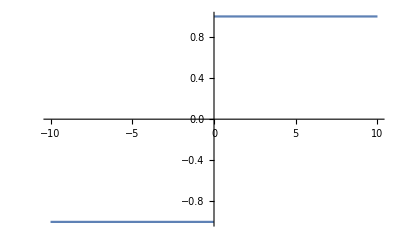

```mathematica
Plot[Abs[x]/x,{x,-10,10}]
```

## Question 2

### a) sec^2(x)

```mathematica
D[Tan[x],x]
```

Sec[x]^2

### b) -e^2/x^2-1/(2 x^(3/2))-4 x^3+3 √5 x^(-1+√5)+2 e^x Log[e]

```mathematica
D[2 e^x+1/(√x)-x^4+3 x^(√5)+π^3+e^2/x,x]
```

-e^2/x^2-1/(2 x^(3/2))-4 x^3+3 √5 x^(-1+√5)+2 e^x Log[e]

### c) 4(7 Cos[7 x]-Sin[x]/2) (Cos[x]/2+Sin[7 x])^3

```mathematica
D[(Sin[7x]+1/2 Cos[x])^4,x]
```

4 (7 Cos[7 x]-Sin[x]/2) (Cos[x]/2+Sin[7 x])^3

## Question 3

### 1) Domain and Range

```mathematica
FunctionDomain[x^3/(x-2),x]
```

x<2||x>2

```mathematica
FunctionRange[x^3/(x-2),x,y]
```

True

Domain is  x < 2 , x > 2. 
Range is unrestricted.  (-∞ , ∞)

### 2) y - intercepts and x - intercepts

[x^3/(-2+x),{x,y}]

There is an intercept at point (0, 0)

### 3) Symmetry

Determine if the function is odd or even.

```mathematica
myEvenFunction[x_]:=x^2/(x-2)
Equal[myEvenFunction[x],myEvenFunction[-x]]
```

x^2/(-2+x)==x^2/(-2-x)

```mathematica
myOddFunction[x_]:=x^2/(x-2)
FullSimplify[ForAll[x,myOddFunction[x]==myOddFunction[-x]]]
```

False

f (x) is an even function since f (-x) =  f (x). Therefore, it is symmetric about the y - axis.

### 4) Vertical and Horizontal Asymptote(s)

Based on the domain, there is a vertical asymptote at x = 2.

### 5) First Derivative: Increase/Decrease and Relative Extrema

```mathematica
Dt[x^2/(x-2),x]
```

(2 x)/(-2+x)-x^2/(-2+x)^2

f’(x) = (2 x)/(-2+x)-x^2/(-2+x)^2
At f’(x) = 0, the critical point is at x = 2. 
For interval (- ∞, 2), choose value x = 1. For interval (2, ∞), choose value x = 5.  At x = 1, the function is decreasing since -3 < 0 . At x = 5, the function is increasing since 5/9 > 0.

```mathematica
f3[x_] :=(2 x)/(-2+x)-x^2/(-2+x)^2
f3[1]
```

-3

```mathematica
f3[5]
```

5/9

### 6) Second Derivative: Concavity and Inflection Points

```mathematica
f3'[x]
```

2/(-2+x)-(4 x)/(-2+x)^2+(2 x^2)/(-2+x)^3

```mathematica
Solve[f3'[x] ==0, x]
```

{}

### 7) Graph the Function

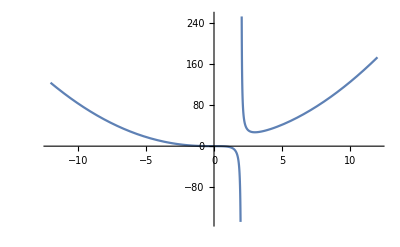

```mathematica
Plot[x^3/(x-2), {x,-12,12}]
```

## Question 4

### a) -(2 x+y)/(x+2 y)

WolframAlphaQueryParseResults

-(2 x+y)/(x+2 y)

### b) y = -2

```mathematica
f4[x_,y_] := -(2 x+y)/(x+2 y)
f4[1, -2]
```

0

The line tangent to the curve at the point (1,-2) is y = -2. At this point, the gradient is 0. Therefore, the slope equals 0, which meant that the line is y= -2.

## Question 5

### a) x = 3, x = -3

```mathematica
f5[x_] := 3x + 27/x
f5'[x]
```

3-27/x^2

```mathematica
Solve[f5'[x] ==0, x]
```

{{x→-3},{x→3}}

There are two critical points at x = -3 and x = 3.

### b) Absolute Minimum at x = 3, y = 18. No local minimum or maximum.

```mathematica
Dt[f5'[x],x]
```

54/x^3

```mathematica
f[x_] := 54/x^3
f[3]
```

2

```mathematica
f5'[3]
```

0

Since at f’’(3) = 2 which is greater than f’(3) = 0, there is an absolute minimum at x = 3.

## Question 6

Equation for Perimeter: 2(x+y) = 30  → y = 15 - x
Equation for Area: xy → x(15 - x)

```mathematica
Dt[15x-x^2, x]
```

15-2 x

```mathematica
Dt[15-2x,x]
```

-2

To be the maximum value possible, dA/dx must equal 0. 
Since - 2 < 0, the area is at its maximum. 
Therefore, 15 - 2x = 0, which meant x = 15/2 , and y = 15/2.

```mathematica
(15/2)^2
```

225/4

The maximum possible area is 225/4 cm^2.

## Question 7

### a)

```mathematica
f7[x_] := x^3 + 5x +7 
Solve[f7[x]==0,x]
```

{{x→Root-1.12Root[7+5 #1+#1^3&,1]-1.1194375270626309},{x→Root0.560-2.44 ⅈRoot[7+5 #1+#1^3&,2]0.5597187635313154},{x→Root0.560+2.44 ⅈRoot[7+5 #1+#1^3&,3]0.5597187635313154}}

```mathematica
N[{{x->Root[7+5 #1+#1^3&,1,0]},{x->Root[7+5 #1+#1^3&,2,0]},{x->Root[7+5 #1+#1^3&,3,0]}}]
```

{{x→-1.11944},{x→0.559719-2.43718 ⅈ},{x→0.559719+2.43718 ⅈ}}

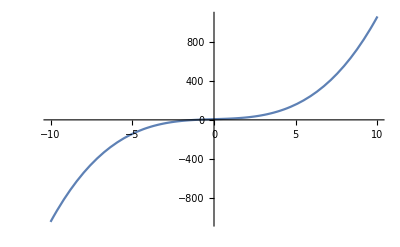

```mathematica
Plot[f7[x],{x,-10,10}]
```

There is one value where x0 = 0. This occur as an x - intercept at x = -1.11944.

```mathematica
f7[-2]
```

-11

```mathematica
f7[-1]
```

1

To show that there is a number x0 which equals 0, two values of x can be used to narrow down the number. Since the function is continuous, there is a number that exists between (-2, 1) such that f(x0) = 0.

### b)

```mathematica
f7[-1.5]
```

-3.875

```mathematica
f7[-1]
```

1

Between the interval of [-1.5, -1] lies a number such that f(x0) = 0.

### c)

```mathematica
Dt[f7[x],x]
```

5+3 x^2

Since the values of f’(x) is greater than 0 for all real value of x, the function is increasing. Therefore, there is only only one intercept.

## Question 8

### a)

```mathematica
Dt[√(1-x),x]
```

-1/(2 √(1-x))

Linear approximation of a f(x) = f(a) + f’(a)(x-a)

```mathematica
√(1-0)+ (-1/(2 √(1-0)))(x-0)
```

1-x/2

### b)

```mathematica
f8[x_] := 1-x/2
f8[0.1]
```

0.95

```mathematica
f8[0.01]
```

0.995

√0.9is approximately 0.95.
√0.99is approximately 0.995.

## Question 9

There are 4 equal intervals. [-1/2,0 ], [0, 1/2],[1/2, 1], and [1, 3/2].  
△x = (b-a)/n=(3/2-(1/2))/4 = 1/2

```mathematica
f9[x_] := 1/(x^4+1)
(1/2)(f9[-1/2]+f9[0]+f9[1/2]+f9[1])
```

115/68

```mathematica
N[115/68]
```

1.69118

The integral is approximately equal to 115/68or 1.69118.

## Question 10

### a) -x^2

```mathematica
D[∫_x^1 t^2 ⅆt,x]
```

-x^2

### b) 1/4 (4 x+4 x Cos[2 x^2])

```mathematica
D[∫_0^(x^2) (Cos[t])^2 ⅆt,x]
```

1/4 (4 x+4 x Cos[2 x^2])

## Question 11

### a) (2 x^(5/2))/5+x^3/3+C

```mathematica
∫x^2(1+1/(√x))ⅆx
```

(2 x^(5/2))/5+x^3/3

### b) 0

```mathematica
∫_-1^1 x^2 Sin[x^3]ⅆx
```

0

## Question 12

```mathematica
p1 = Plot[4x^2,{x,-2,2}]
p2 = Plot[(x^2) +3,{x,-2,2}]
```

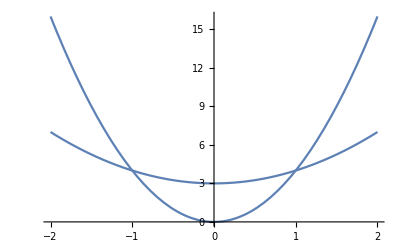

```mathematica
Show[p1, p2]
```

```mathematica
f1[x_]:=4x^2;
g1[x_]:=(x^2)+3;
```

```mathematica
sol=NSolve[f1[x]==g1[x],x]
```

{{x→-1.},{x→1.}}

```mathematica
{a,b}=x/.sol
```

{-1.,1.}

```mathematica
Integrate[g1[x]-f1[x],{x,a,b}]
```

4.

The area bounded by the two curves is equal to 4.